```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression,100000];Length[deps3]
```

100000

```mathematica
Take[deps3,5]
```

{{2,3,{3,{3,2,1,5,4},{2<->4,2<->5},{{2,3,4},{2,4,5},{1,2,5}}}},{3,6,{3,{2,5,4,3,1},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}},{3,5,{3,{1,2,3,6,5},{2<->5,2<->6},{{1,2,5},{2,5,6},{2,3,6}}}},{3,7,{3,{1,5,4,6,2},{2<->5,5<->6},{{1,2,5},{2,5,6},{4,5,6}}}},{3,9,{3,{2,6,5,4,3},{3<->6,4<->6},{{2,3,6},{3,4,6},{4,5,6}}}}}

```mathematica
Take[deps3,5]
```

{{2,3,{3,{2,5,4,1,3},{2<->4,2<->5},{{2,3,4},{2,4,5},{1,2,5}}}},{3,6,{3,{5,3,1,4,2},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}},{3,5,{3,{2,6,5,3,1},{2<->5,2<->6},{{1,2,5},{2,5,6},{2,3,6}}}},{3,7,{3,{5,6,2,4,1},{2<->5,5<->6},{{1,2,5},{2,5,6},{4,5,6}}}},{3,9,{3,{6,4,3,5,2},{3<->6,4<->6},{{2,3,6},{3,4,6},{4,5,6}}}}}

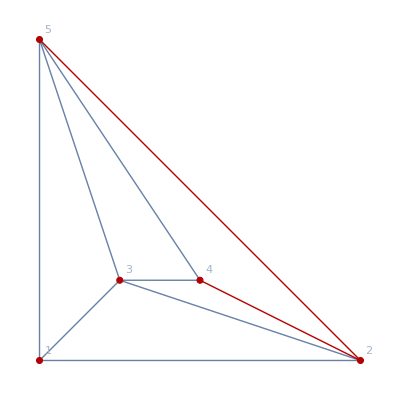
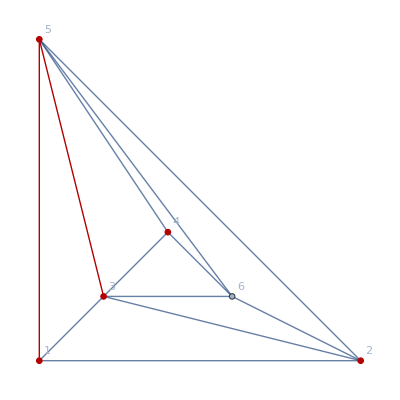
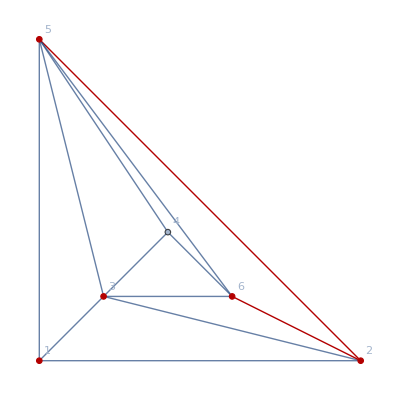
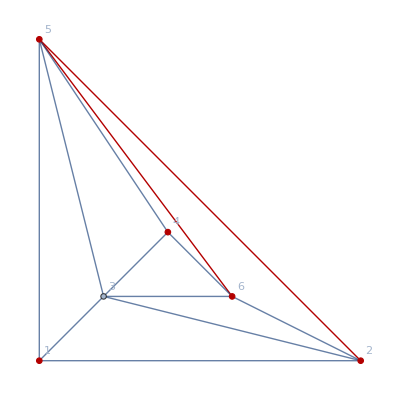
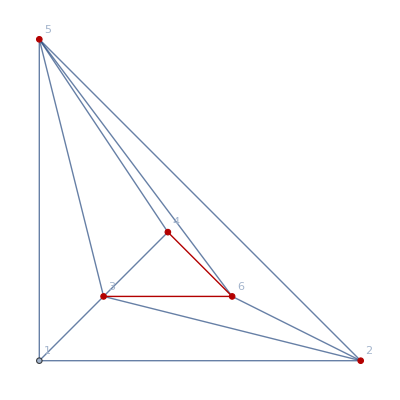

```mathematica
Map[With[
{g=ReadGrof[#[[1]]]},
Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding", GraphHighlight->Join[#[[3,2]],#[[3,3]]]]]&,
Take[deps3,5]
]
```

```mathematica
GenGraphs[g_,vertices_]:=Block[
{couples=Join[
Table[{i,Mod[i+2,5]+1},{i,1,5}],
Table[{i,Mod[i+3,5]+1},{i,1,5}]
]},
couples=DeleteDuplicates[Map[Sort[#]&,couples]];
couples=Map[vertices[[#[[1]]]]<->vertices[[#[[2]]]]&,couples];
Map[EdgeAdd[g,#]&,couples]
]
```

```mathematica
Chrom4[g_]:=ChromaticPolynomial[g,4]/24
```

```mathematica
GenDoubleGraphs[g_,vertices_]:=Block[
{couples=Table[{vertices[[i]]<->vertices[[Mod[i+2,5]+1]],vertices[[i]]<->vertices[[Mod[i+3,5]+1]]},{i,1,5}]},
couples=DeleteDuplicates[Map[Sort[#]&,couples]];
Map[EdgeAdd[g,#]&,couples]
]
```

```mathematica
GenDoubleGraphs2[g_,vertices_]:=Block[
{couples=Table[{vertices[[i]]<->vertices[[Mod[i+2,5]+1]],vertices[[i]]<->vertices[[Mod[i+3,5]+1]]},{i,1,5}]},
couples=Map[Sort[#]&,couples];
Map[{#,EdgeAdd[g,#]//Chrom4,EdgeAdd[g,#[[1]]]//Chrom4,EdgeAdd[g,#[[2]]]//Chrom4}&,couples]
]
```

```mathematica
{{2,3,6},{3,4,6},{4,5,6}}
```

```mathematica
MatrixForm[GenMatrix[EdgeDelete[ReadGrof[3],{3<->6,4<->6}],{6,4,3,5,2}]]
```

(4 | 3 | 2 | 4 | 4
3 | 2 | 4 | 4 | 2
2 | 4 | 2 | 4 | 4
4 | 4 | 4 | 4 | 4
4 | 2 | 4 | 4 | 4)

```mathematica
3,9,{3,{6,4,3,5,2},{3<->6,4<->6}
```

```mathematica
GenMatrix[g_,vertices_]:=Block[
{result=Table[-1,{i,1,6},{j,1,6}],i,j, v1, v2, graph2,vert, div},
For[i=1,i≤5,i++,
v1=vertices[[i]];
For[j=1,j≤i,j++,
v2=vertices[[j]];
If[i==j,
vert={v1<->vertices[[Mod[i+1,5]+1]],v1<->vertices[[Mod[i+2,5]+1]]};
graph2=EdgeAdd[g,vert];
result[[i,j]]=ChromaticPolynomial[graph2,4]/24
,
graph2=EdgeAdd[g,v1<->v2];
result[[i,j]]=ChromaticPolynomial[graph2,4]/24;
result[[j,i]]=result[[i,j]]
]
];
];
div=result[[1,2]];
For[i=1,i≤5,i++,
result[[i,6]]=Sum[result[[i,k]],{k,1,5}]-result[[i,i]]-2*result[[i,Mod[i,5]+1]];
result[[6,i]]=Sum[result[[k,i]],{k,1,5}]-result[[i,i]]-2*result[[Mod[i,5]+1,i]];
];

result[[6,6]]=Sum[result[[6,k]],{k,1,5}]/div;
For[i=1,i≤5,i++,
result[[i,i]]=Style[result[[i,i]],Bold, Red];
result[[i,Mod[i,5]+1]]=Style[result[[i,Mod[i,5]+1]],Italic, Blue];
result[[i,Mod[i+3,5]+1]]=Style[result[[i,Mod[i+3,5]+1]],Italic,Blue];
];
result]
```

```mathematica
TableForm[
Map[With[
{g=EdgeDelete[ReadGrof[#[[1]]],#[[3,3]]]},
Join[
{Graph[g,GraphHighlight->#[[3,2]],VertexLabels->"Name",ImageSize->100,GraphLayout->"PlanarEmbedding",PlotLabel->ChromaticPolynomial[g,4]/24],
Graph[ReadGrof[#[[1]]],GraphLayout->"PlanarEmbedding",ImageSize->100,PlotLabel->ChromaticPolynomial[ReadGrof[#[[1]]],4]/24],
Graph[ReadGrof[#[[2]]],GraphLayout->"PlanarEmbedding",ImageSize->100,PlotLabel->ChromaticPolynomial[ReadGrof[#[[2]]],4]/24]
},
{#[[3,3]],#[[3,2]]},
{
MatrixForm[GenMatrix[g,#[[3,2]]], TableHeadings->{Range[5],Range[5]}]
}
]
]&,
Take[Select[Take[deps3,100],Chrom[#[[1]]]<=Chrom[#[[2]]]&],-20]
],
TableDepth->3
]
```

-Graphics- | -Graphics- | -Graphics- | {5<->6}
{6<->8} | {4}
{6}
{3}
{8}
{5} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 4 | 4 | 2 | 4
2 | 4 | 1 | 4 | 3 | 2
3 | 4 | 4 | 4 | 4 | 4
4 | 2 | 3 | 4 | 1 | 4
5 | 4 | 2 | 4 | 4 | 2)
-Graphics- | -Graphics- | -Graphics- | {1<->7}
{3<->7} | {2}
{7}
{5}
{3}
{1} | ( | 1 | 2 | 3 | 4 | 5
1 | 4 | 4 | 4 | 4 | 4
2 | 4 | 1 | 4 | 2 | 3
3 | 4 | 4 | 2 | 4 | 2
4 | 4 | 2 | 4 | 2 | 4
5 | 4 | 3 | 2 | 4 | 1)
-Graphics- | -Graphics- | -Graphics- | {2<->7}
{5<->7} | {1}
{7}
{3}
{5}
{2} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 4 | 4 | 2 | 4
2 | 4 | 1 | 4 | 3 | 2
3 | 4 | 4 | 4 | 4 | 4
4 | 2 | 3 | 4 | 1 | 4
5 | 4 | 2 | 4 | 4 | 2)
-Graphics- | -Graphics- | -Graphics- | {2<->7}
{1<->7} | {5}
{7}
{3}
{1}
{2} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 4 | 4 | 2 | 4
2 | 4 | 1 | 4 | 3 | 2
3 | 4 | 4 | 4 | 4 | 4
4 | 2 | 3 | 4 | 1 | 4
5 | 4 | 2 | 4 | 4 | 2)
-Graphics- | -Graphics- | -Graphics- | {5<->7}
{3<->7} | {2}
{7}
{1}
{3}
{5} | ( | 1 | 2 | 3 | 4 | 5
1 | 4 | 4 | 4 | 4 | 4
2 | 4 | 1 | 4 | 2 | 3
3 | 4 | 4 | 2 | 4 | 2
4 | 4 | 2 | 4 | 2 | 4
5 | 4 | 3 | 2 | 4 | 1)
-Graphics- | -Graphics- | -Graphics- | {3<->8}
{6<->8} | {2}
{8}
{5}
{6}
{3} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 4 | 4 | 2 | 4
2 | 4 | 1 | 4 | 3 | 2
3 | 4 | 4 | 4 | 4 | 4
4 | 2 | 3 | 4 | 1 | 4
5 | 4 | 2 | 4 | 4 | 2)
-Graphics- | -Graphics- | -Graphics- | {6<->8}
{5<->8} | {3}
{8}
{2}
{5}
{6} | ( | 1 | 2 | 3 | 4 | 5
1 | 4 | 4 | 4 | 4 | 4
2 | 4 | 1 | 4 | 2 | 3
3 | 4 | 4 | 2 | 4 | 2
4 | 4 | 2 | 4 | 2 | 4
5 | 4 | 3 | 2 | 4 | 1)
-Graphics- | -Graphics- | -Graphics- | {3<->4}
{3<->8} | {5}
{3}
{2}
{8}
{4} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)
-Graphics- | -Graphics- | -Graphics- | {3<->4}
{4<->8} | {5}
{4}
{6}
{8}
{3} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)
-Graphics- | -Graphics- | -Graphics- | {3<->5}
{3<->7} | {4}
{3}
{1}
{7}
{5} | ( | 1 | 2 | 3 | 4 | 5
1 | 12 | 14 | 13 | 13 | 14
2 | 14 | 4 | 14 | 6 | 12
3 | 13 | 14 | 5 | 14 | 6
4 | 13 | 6 | 14 | 5 | 14
5 | 14 | 12 | 6 | 14 | 4)
-Graphics- | -Graphics- | -Graphics- | {3<->5}
{5<->7} | {4}
{5}
{2}
{7}
{3} | ( | 1 | 2 | 3 | 4 | 5
1 | 1 | 10 | 2 | 9 | 10
2 | 10 | 4 | 10 | 6 | 8
3 | 2 | 10 | 2 | 10 | 10
4 | 9 | 6 | 10 | 5 | 10
5 | 10 | 8 | 10 | 10 | 8)
-Graphics- | -Graphics- | -Graphics- | {4<->5}
{5<->6} | {3}
{5}
{2}
{6}
{4} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)
-Graphics- | -Graphics- | -Graphics- | {4<->5}
{4<->6} | {3}
{4}
{8}
{6}
{5} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)
-Graphics- | -Graphics- | -Graphics- | {5<->6}
{2<->6} | {4}
{6}
{8}
{2}
{5} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)
-Graphics- | -Graphics- | -Graphics- | {4<->6}
{6<->8} | {5}
{6}
{2}
{8}
{4} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)
-Graphics- | -Graphics- | -Graphics- | {1<->7}
{3<->7} | {2}
{7}
{5}
{3}
{1} | ( | 1 | 2 | 3 | 4 | 5
1 | 16 | 16 | 16 | 16 | 16
2 | 16 | 4 | 16 | 8 | 12
3 | 16 | 16 | 8 | 16 | 8
4 | 16 | 8 | 16 | 8 | 16
5 | 16 | 12 | 8 | 16 | 4)
-Graphics- | -Graphics- | -Graphics- | {6<->8}
{4<->8} | {2}
{8}
{3}
{4}
{6} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)
-Graphics- | -Graphics- | -Graphics- | {3<->4}
{3<->6} | {5}
{3}
{2}
{6}
{4} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 10 | 2 | 10 | 10
2 | 10 | 4 | 10 | 8 | 6
3 | 2 | 10 | 1 | 10 | 9
4 | 10 | 8 | 10 | 8 | 10
5 | 10 | 6 | 9 | 10 | 5)
-Graphics- | -Graphics- | -Graphics- | {4<->5}
{5<->6} | {3}
{5}
{8}
{6}
{4} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 10 | 2 | 10 | 10
2 | 10 | 4 | 10 | 8 | 6
3 | 2 | 10 | 1 | 10 | 9
4 | 10 | 8 | 10 | 8 | 10
5 | 10 | 6 | 9 | 10 | 5)
-Graphics- | -Graphics- | -Graphics- | {2<->6}
{2<->8} | {3}
{2}
{7}
{8}
{6} | ( | 1 | 2 | 3 | 4 | 5
1 | 2 | 6 | 6 | 2 | 6
2 | 6 | 4 | 6 | 5 | 5
3 | 6 | 6 | 2 | 6 | 2
4 | 2 | 5 | 6 | 1 | 6
5 | 6 | 5 | 2 | 6 | 1)

```mathematica
Graph[ReadGrof[3],GraphHighlight->{6,4,3,5,2,3<->6,4<->6}, VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

-Graphics-

```mathematica
EdgeList[ReadGrof[2]]
```

{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

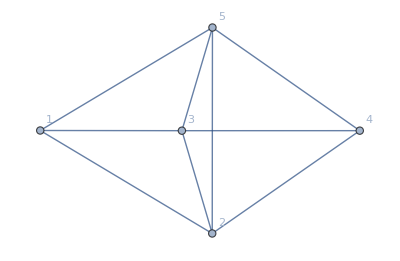

```mathematica
Graph[ReadGrof[2], VertexLabels->"Name"]
```

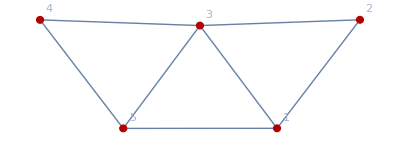

```mathematica
Graph[EdgeDelete[ReadGrof[2],{2<->4,2<->5}],GraphHighlight->{2,5,4,1,3}, VertexLabels->"Name"]
```

{2<->5,2<->4,2<->1,2<->3,5<->4,5<->1,5<->3,4<->1,4<->3,1<->3}

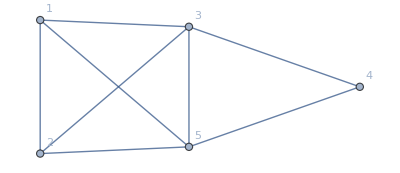
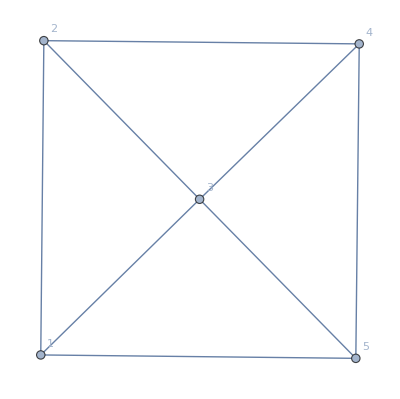
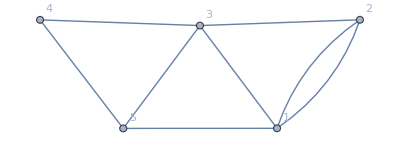
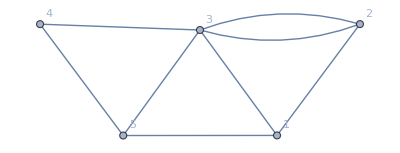
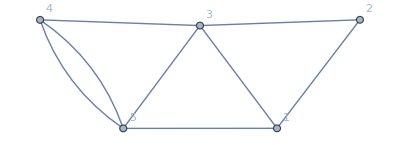
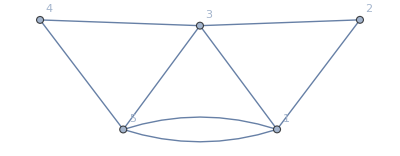
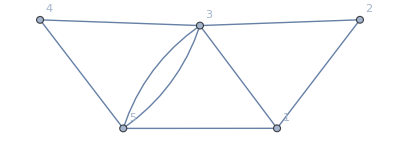
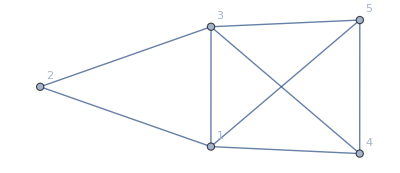

```mathematica
With[
{g=EdgeDelete[ReadGrof[2],{2<->4,2<->5}]},
Map[Graph[#, VertexLabels->"Name"]&,GenDoubleGraphs[g,{2,5,4,1,3}]]
]
```

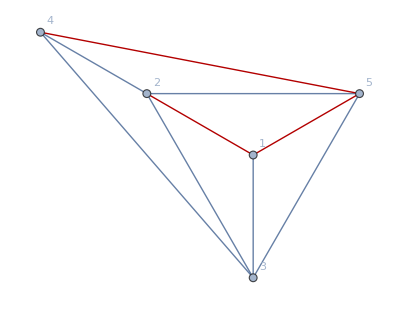

```mathematica
Graph[ReadGrof[2],GraphHighlight->{1<->5,4<->5,4<->6,6<->2,2<->1}, VertexLabels->"Name", GraphLayout->"RadialDrawing"]
```